# Physics 20

## Assignment 5 - Mathematica

## Shubh Agrawal

## Part 2- Analysis of trigonometric Taylor expansions:

### Error analysis of sine and cosine expansions:

We define the functions representing the Taylor (or Maclaurin) series of the sine and cosine functions around x = 0 :

```mathematica
SerCos[x_,n_]:= Normal[Series[Cos[y], {y, 0, n}]]/. y-> x
```

```mathematica
SerSin[x_,n_]:= Normal[Series[Sin[y], {y, 0, n}]]/.y->x
```

Evaluating the series approximations at some discrete values of x and n, we get:

```mathematica
SerCos[x, 5]
```

1-x^2/2+x^4/24

```mathematica
SerSin[x, 10]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
SerCos[0.5, 6]
```

0.877582

Plotting the function approximations against input, we have:

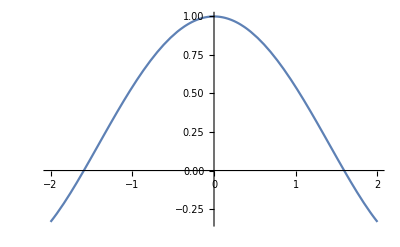

```mathematica
Plot[SerCos[x, 5], {x, -2, 2}]
```

```mathematica
Manipulate[Plot[SerSin[x,n], {x, -Pi, Pi}], {n, 1, 10, 1}]
```

For analyzing the errors using the built-in Mathematica trigonometric functions, we define the “delta” functions:

```mathematica
DeltaSin[x_, n_]:= N[SerSin[x, n]- Sin[x]]
```

```mathematica
DeltaCos[x_, n_]:= N[SerCos[x, n]- Cos[x]]
```

So, for discrete values of input and degree, we have:

```mathematica
DeltaSin[1, 5]
```

0.000195682

```mathematica
DeltaSin[4, 5]
```

2.62347

```mathematica
DeltaSin[1, 15]
```

-2.77556×10^-15

```mathematica
DeltaCos[Pi, 8]
```

0.0239778

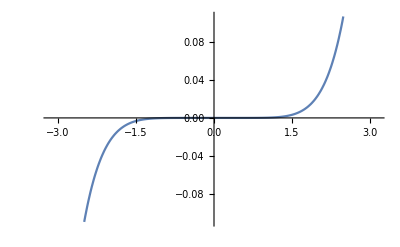

```mathematica
Plot[DeltaSin[x, 5], {x, -Pi, Pi}]
```

```mathematica
Manipulate[Plot[DeltaSin[x,n], {x, -2*Pi, 2*Pi}], {n, 1, 20, 1}]
```

We note that, for odd degree Taylor expansions, the error sign is positive for positive inputs, and vice versa. Additionally, the error curve is symmetric about the origin.

### Behavior of trigonometric square sum identity:

First, we take the previously defining Maclaurin expansions of cosine and sine, and raise their expressions to the second power:

```mathematica
SumOfSquared[x_, n_]:= SerSin[x,n]^2+SerCos[x,n]^2
```

We find the algebraic results, both dependent on the variable and at discrete values, to note the dependency on the degree of the expansion:

```mathematica
SumOfSquared[x, 8]
```

(x-0.166667 x^3+0.00833333 x^5-0.000198413 x^7)^2+(1.-0.5 x^2+0.0416667 x^4-0.00138889 x^6+0.0000248016 x^8)^2

```mathematica
SumOfSquared[1.5, 8]
```

0.999795

```mathematica
SumOfSquared[4, 4]
```

57.8889

To analyze behavior graphically, we use a plot of the sum of squares (squared series)against input, with variable expansion degree:

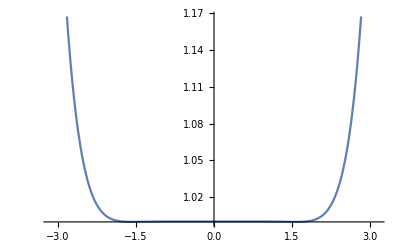

```mathematica
Plot[SumOfSquared[x, 7], {x, -Pi, Pi}]
```

```mathematica
Manipulate[Plot[SumOfSquared[x,n], {x, -2*Pi, 2*Pi}], {n, 1, 20, 1}]
```

Note that the value of sum is symmetric about the y-axis, i.e., about x = 0, which is the point we took our Taylor expansion about.

We do a similar analysis for the SumOfSquares[x, n] function, representing the sum of the series approximation of the squares of sine and cosine, defined as follows:

```mathematica
SerCosSq[x_,n_]:= Normal[Series[Cos[y]*Cos[y], {y, 0, n}]]/. y-> x
```

```mathematica
SerSinSq[x_,n_]:= Normal[Series[Sin[y]* Sin[y], {y, 0, n}]]/. y-> x
```

```mathematica
SumOfSquares[x_,n_] := SerSinSq[x,n] + SerCosSq[x, n]
```

```mathematica
Manipulate[Plot[SumOfSquared[x,n], {x, -10*Pi, 10*Pi}], {n, 1, 10, 1}]
```

Note that this approximation is more accurate for a larger range (one order of magnitude difference) and the nature of the error is also consistent for varying parity of degree n.

## Part 3- Euler Angles and Rotation Matrices:

Defining three-dimensional rotation matrices, we have them as follows:

```mathematica
Subscript[R, x][Θ_]:= {{1,0,0},{0, Cos[Θ],-Sin[Θ]},{0,Sin[Θ],Cos[Θ]}}
```

```mathematica
Subscript[R, y][ζ_]:={{Cos[ζ],0,Sin[ζ]},{0,1,0},{-Sin[ζ],0,Cos[ζ]}}
```

```mathematica
Subscript[R, z][∅_]:={{Cos[∅],-Sin[∅],0},{Sin[∅],Cos[∅],0},{0,0,1}}
```

```mathematica
Subscript[R, x][0]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[Subscript[R, z][Pi/4]]
```

(1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1)

For the General Three-dimensional Rotation Matrix, we define and then simply the product of these three rotational matrices:

```mathematica
Rot3[Ψ_,Θ_,∅_] := Subscript[R, z][Ψ].Subscript[R, x][Θ].Subscript[R, z][∅]
```

```mathematica
Simplify[Rot3[Ψ,Θ,∅]]
```

{{Cos[Ψ] Cos[∅]-Cos[Θ] Sin[Ψ] Sin[∅],-Cos[Θ] Cos[∅] Sin[Ψ]-Cos[Ψ] Sin[∅],Sin[Θ] Sin[Ψ]},{Cos[∅] Sin[Ψ]+Cos[Θ] Cos[Ψ] Sin[∅],Cos[Θ] Cos[Ψ] Cos[∅]-Sin[Ψ] Sin[∅],-Cos[Ψ] Sin[Θ]},{Sin[Θ] Sin[∅],Cos[∅] Sin[Θ],Cos[Θ]}}

```mathematica
FullSimplify[Rot3[Ψ,Θ,∅]]
```

{{Cos[Ψ] Cos[∅]-Cos[Θ] Sin[Ψ] Sin[∅],-Cos[Θ] Cos[∅] Sin[Ψ]-Cos[Ψ] Sin[∅],Sin[Θ] Sin[Ψ]},{Cos[∅] Sin[Ψ]+Cos[Θ] Cos[Ψ] Sin[∅],Cos[Θ] Cos[Ψ] Cos[∅]-Sin[Ψ] Sin[∅],-Cos[Ψ] Sin[Θ]},{Sin[Θ] Sin[∅],Cos[∅] Sin[Θ],Cos[Θ]}}

```mathematica
MatrixForm[%]
```

(Cos[Ψ] Cos[∅]-Cos[Θ] Sin[Ψ] Sin[∅] | -Cos[Θ] Cos[∅] Sin[Ψ]-Cos[Ψ] Sin[∅] | Sin[Θ] Sin[Ψ]
Cos[∅] Sin[Ψ]+Cos[Θ] Cos[Ψ] Sin[∅] | Cos[Θ] Cos[Ψ] Cos[∅]-Sin[Ψ] Sin[∅] | -Cos[Ψ] Sin[Θ]
Sin[Θ] Sin[∅] | Cos[∅] Sin[Θ] | Cos[Θ])

Note that the sequential matrix representation of rotation can be simplified to a single three-dimensional rotation matrix expressible as trigonometric ratios of the three Euler angles.

For the manual expression for inverse rotation matrix (undoing the rotations one-by-one), we get the matrix:

```mathematica
Rot3Inverse[Ψ_,Θ_,∅_] := Subscript[R, z][-∅].Subscript[R, x][-Θ].Subscript[R, z][-Ψ]
```

```mathematica
Rot3Inverse[ψ,θ,φ].Rot3[ψ,θ,φ]
```

{{Sin[θ]^2 Sin[φ]^2+(Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ])^2+(Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ])^2,Cos[φ] Sin[θ]^2 Sin[φ]+(Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ]) (Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ])+(-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]) (Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]),Cos[θ] Sin[θ] Sin[φ]-Cos[ψ] Sin[θ] (Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ])+Sin[θ] Sin[ψ] (Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ])},{Cos[φ] Sin[θ]^2 Sin[φ]+(Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ]) (Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ])+(-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]) (Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]),Cos[φ]^2 Sin[θ]^2+(-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ])^2+(Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ])^2,Cos[θ] Cos[φ] Sin[θ]+Sin[θ] Sin[ψ] (-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ])-Cos[ψ] Sin[θ] (Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ])},{Cos[θ] Sin[θ] Sin[φ]-Cos[ψ] Sin[θ] (Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ])+Sin[θ] Sin[ψ] (Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]),Cos[θ] Cos[φ] Sin[θ]+Sin[θ] Sin[ψ] (-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ])-Cos[ψ] Sin[θ] (Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ]),Cos[θ]^2+Cos[ψ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ψ]^2}}

```mathematica
Simplify[%]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Using the built-in matrix inverse function, we derive the result as follows:

```mathematica
Inverse[Rot3[Ψ,Θ,∅]]
```

{{(Cos[Θ]^2 Cos[Ψ] Cos[∅]+Cos[Ψ] Cos[∅] Sin[Θ]^2-Cos[Θ] Sin[Ψ] Sin[∅])/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2),(Cos[Θ]^2 Cos[∅] Sin[Ψ]+Cos[∅] Sin[Θ]^2 Sin[Ψ]+Cos[Θ] Cos[Ψ] Sin[∅])/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2),(Cos[Ψ]^2 Sin[Θ] Sin[∅]+Sin[Θ] Sin[Ψ]^2 Sin[∅])/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2)},{(-Cos[Θ] Cos[∅] Sin[Ψ]-Cos[Θ]^2 Cos[Ψ] Sin[∅]-Cos[Ψ] Sin[Θ]^2 Sin[∅])/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2),(Cos[Θ] Cos[Ψ] Cos[∅]-Cos[Θ]^2 Sin[Ψ] Sin[∅]-Sin[Θ]^2 Sin[Ψ] Sin[∅])/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2),(Cos[Ψ]^2 Cos[∅] Sin[Θ]+Cos[∅] Sin[Θ] Sin[Ψ]^2)/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2)},{(Cos[∅]^2 Sin[Θ] Sin[Ψ]+Sin[Θ] Sin[Ψ] Sin[∅]^2)/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2),(-Cos[Ψ] Cos[∅]^2 Sin[Θ]-Cos[Ψ] Sin[Θ] Sin[∅]^2)/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2),(Cos[Θ] Cos[Ψ]^2 Cos[∅]^2+Cos[Θ] Cos[∅]^2 Sin[Ψ]^2+Cos[Θ] Cos[Ψ]^2 Sin[∅]^2+Cos[Θ] Sin[Ψ]^2 Sin[∅]^2)/(Cos[Θ]^2 Cos[Ψ]^2 Cos[∅]^2+Cos[Ψ]^2 Cos[∅]^2 Sin[Θ]^2+Cos[Θ]^2 Cos[∅]^2 Sin[Ψ]^2+Cos[∅]^2 Sin[Θ]^2 Sin[Ψ]^2+Cos[Θ]^2 Cos[Ψ]^2 Sin[∅]^2+Cos[Ψ]^2 Sin[Θ]^2 Sin[∅]^2+Cos[Θ]^2 Sin[Ψ]^2 Sin[∅]^2+Sin[Θ]^2 Sin[Ψ]^2 Sin[∅]^2)}}

```mathematica
Simplify[%.Rot3[Ψ,Θ,∅]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Distinctly evaluating the difference in the two inverse rotation matrix expressions can be written as:

```mathematica
Rot3Inverse[ψ,θ,φ] - Inverse[Rot3[ψ,θ,φ]]
```

{{Cos[φ] Cos[ψ]-Cos[θ] Sin[φ] Sin[ψ]-(Cos[θ]^2 Cos[φ] Cos[ψ]+Cos[φ] Cos[ψ] Sin[θ]^2-Cos[θ] Sin[φ] Sin[ψ])/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2),Cos[θ] Cos[ψ] Sin[φ]+Cos[φ] Sin[ψ]-(Cos[θ] Cos[ψ] Sin[φ]+Cos[θ]^2 Cos[φ] Sin[ψ]+Cos[φ] Sin[θ]^2 Sin[ψ])/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2),Sin[θ] Sin[φ]-(Cos[ψ]^2 Sin[θ] Sin[φ]+Sin[θ] Sin[φ] Sin[ψ]^2)/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)},{-Cos[ψ] Sin[φ]-Cos[θ] Cos[φ] Sin[ψ]-(-Cos[θ]^2 Cos[ψ] Sin[φ]-Cos[ψ] Sin[θ]^2 Sin[φ]-Cos[θ] Cos[φ] Sin[ψ])/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2),Cos[θ] Cos[φ] Cos[ψ]-Sin[φ] Sin[ψ]-(Cos[θ] Cos[φ] Cos[ψ]-Cos[θ]^2 Sin[φ] Sin[ψ]-Sin[θ]^2 Sin[φ] Sin[ψ])/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2),Cos[φ] Sin[θ]-(Cos[φ] Cos[ψ]^2 Sin[θ]+Cos[φ] Sin[θ] Sin[ψ]^2)/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)},{Sin[θ] Sin[ψ]-(Cos[φ]^2 Sin[θ] Sin[ψ]+Sin[θ] Sin[φ]^2 Sin[ψ])/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2),-Cos[ψ] Sin[θ]-(-Cos[φ]^2 Cos[ψ] Sin[θ]-Cos[ψ] Sin[θ] Sin[φ]^2)/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2),Cos[θ]-(Cos[θ] Cos[φ]^2 Cos[ψ]^2+Cos[θ] Cos[ψ]^2 Sin[φ]^2+Cos[θ] Cos[φ]^2 Sin[ψ]^2+Cos[θ] Sin[φ]^2 Sin[ψ]^2)/(Cos[θ]^2 Cos[φ]^2 Cos[ψ]^2+Cos[φ]^2 Cos[ψ]^2 Sin[θ]^2+Cos[θ]^2 Cos[ψ]^2 Sin[φ]^2+Cos[ψ]^2 Sin[θ]^2 Sin[φ]^2+Cos[θ]^2 Cos[φ]^2 Sin[ψ]^2+Cos[φ]^2 Sin[θ]^2 Sin[ψ]^2+Cos[θ]^2 Sin[φ]^2 Sin[ψ]^2+Sin[θ]^2 Sin[φ]^2 Sin[ψ]^2)}}

```mathematica
Simplify[%]
```

{{0,0,0},{0,0,0},{0,0,0}}

As the difference gives us the zero matrix (of order three), we conclude that either method gives us the same inverse rotation matrix expression.